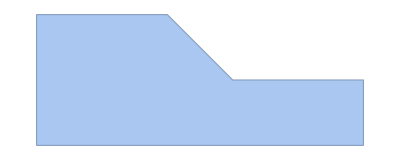

ElementMesh[{{0.,50.},{0.,20.}},{TriangleElement[<115>]}]

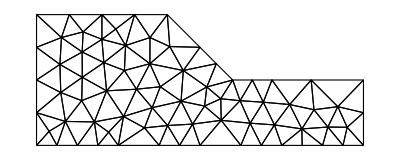

ElementMesh[{{0.,50.},{0.,20.}},{QuadElement[<247>]}]

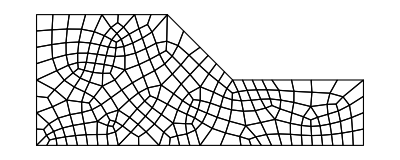

```mathematica
<<NDSolve`FEM`
Needs["MeshTools`"]
(*Create MeshRegion object from Graphics.*)
region=DiscretizeGraphics[Polygon[{{0,0},{50,0},{50,10},{30,10},{20,20},{0,20}}]]
(*Convert MeshRegion object to ElementMesh object and smoothen mesh (improve quality).*)
meshTri=SmoothenMesh@ToElementMesh[region,"MeshOrder"->2,MaxCellMeasure->10,"NodeReordering"->True]
meshTri["Wireframe"]
(*Convert triangular mesh to quadrilateral and smoothen it again.*)
meshQuad=SmoothenMesh@TriangleToQuadMesh@meshTri
meshQuad["Wireframe"]
(*Extrude 2D quadrilateral mesh to 3D hexahedral mesh (with 8 layers).*)
(*mesh3D=ExtrudeMesh[meshQuad,20,10];
mesh3D["Wireframe"["MeshElementStyle"->FaceForm@LightBlue]]*)
```

```mathematica
nodes=meshQuad["Coordinates"];
topol=meshQuad["MeshElements"][[1,1]];
no=Table[{nodes[[i]][[1]],nodes[[i]][[2]],0},{i,1,Length[nodes]}];
no=Table[PrependTo[no[[i]],i],{i,1,Length[no]}];
to=Table[PrependTo[topol[[i]],i],{i,1,Length[topol]}];
```

/home/diogo/projects/dcproj

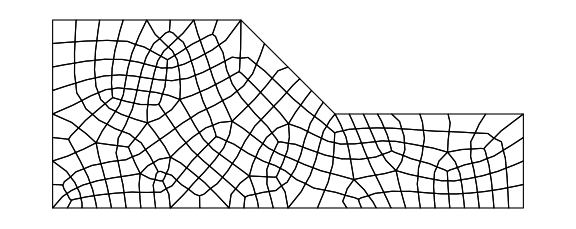

```mathematica
SetDirectory[NotebookDirectory[]]
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis,v},If[order==1,v={1,2,3,4},v={1,5,2,6,3,7,4,8}];
nodes2=Table[{nodes[[i]][[1]],nodes[[i]][[2]]},{i,1,Length[nodes]}];
meshvis=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nodes2,Polygon[topology[[All,v]]]]}];
(*nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];*)
nodevis=Graphics[{MapIndexed[Style[Text[#2[[1]],#1,{-1.8,1.8}],FontSize->9]&,nodes2],{PointSize[Large],Black,Point[nodes2]}}];
{meshvis,nodevis}
];
meshnodes=Import["meshcoords.txt","Table"];
meshtopology=Import["meshtopology.txt","Table"];
order=2;
{meshvis,nodevis}=GenerateGraphics[meshnodes,meshtopology+1,order];(*Generates graphics to visualize mesh*)
Show[meshvis,AspectRatio->Automatic,ImageSize->Large]
```

```mathematica
topol;
```

```mathematica
to;
```

```mathematica
Export["/home/diogo/projects/dcproj/nodes.dat",no]
Export["/home/diogo/projects/dcproj/topol.dat",to]
```

/home/diogo/projects/dcproj/nodes.dat

/home/diogo/projects/dcproj/topol.dat

```mathematica
to[[2]]
```

{1,143,24,144,419,558,559,560,555}

```mathematica
meshtopology[[1]]
```

{26,142,418,145,553,554,555,556}

```mathematica
meshnodes[[1]]
```

{11.3674,7.27909,0}

```mathematica
to[[1]]
```

{0,27,143,419,146,554,555,556,557}

```mathematica
Min[to]
```

0

```mathematica
ss={1./4.*(1.-eta)*(1.-xi)*(-1.-eta-xi),
1./4.*(1.-eta)*(1.+xi)*(-1.-eta+xi),
1./4.*(1.+eta)*(1.+xi)*(-1.+eta+xi),
1./4.*(1.+eta)*(1.-xi)*(-1.+eta-xi),
1./2.*(1.-eta)*(1-xi*xi),
1./2.*(1.-eta*eta)*(1.+xi),
1./2.*(1.+eta)*(1.-xi*xi),
1./2.*(1.-eta*eta)*(1.-xi)}
```

{0.25 (1.-eta) (1.-xi) (-1.-eta-xi),0.25 (1.-eta) (1.+xi) (-1.-eta+xi),0.25 (1.+eta) (1.+xi) (-1.+eta+xi),0.25 (1.+eta) (1.-xi) (-1.+eta-xi),0.5 (1.-eta) (1-xi^2),0.5 (1.-eta^2) (1.+xi),0.5 (1.+eta) (1.-xi^2),0.5 (1.-eta^2) (1.-xi)}

{-1/4 (-1+eta) (-1+xi) (1+eta+xi),1/4 (-1+eta) (1+eta-xi) (1+xi),1/4 (1+eta) (1+xi) (-1+eta+xi),1/4 (1+eta) (-1+xi) (1-eta+xi),1/2 (-1+eta) (-1+xi^2),-1/2 (-1+eta^2) (1+xi),-1/2 (1+eta) (-1+xi^2),1/2 (-1+eta^2) (-1+xi)}

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0}}

QuadElement[{{1,2,3,4,5,6,7,8}}]

ElementMesh[{{-1.,1.},{-1.,1.}},{QuadElement[<1>]}]

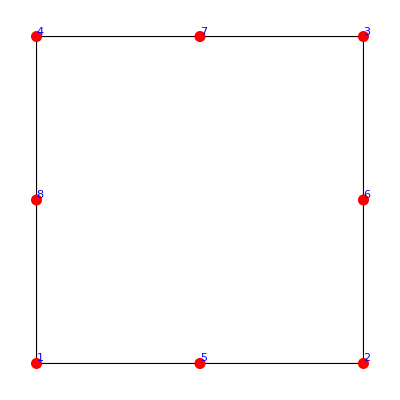

```mathematica
elementOrder=2;
sss=ElementShapeFunction[QuadElement,elementOrder][xi,eta]//Simplify
c=MeshElementBaseCoordinates[QuadElement,2]
e=QuadElement[{MeshElementBaseIncidents[QuadElement,2]}]
mesh=ToElementMesh["Coordinates"->c,"MeshElements"->{e}]
Show[mesh["Wireframe"],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementStyle"->Directive[Red,PointSize[0.02]],"MeshElementIDStyle"->Blue]]]
```

```mathematica
Simplify[ss-sss]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
MeshElementBaseCoordinates[QuadElement,2]
```

{{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0}}

```mathematica
to
```

{{1,27,143,419,146,554,555,556,557},{2,143,24,144,419,558,559,560,555},{3,419,144,25,145,560,561,562,563},{4,146,419,145,26,556,563,564,565},{5,77,147,420,150,566,567,568,569},{6,147,78,148,420,570,571,572,567},{7,420,148,80,149,572,573,574,575},{8,150,420,149,81,568,575,576,577},{9,69,151,421,154,578,579,580,581},{10,151,71,152,421,582,583,584,579},{11,421,152,67,153,584,585,586,587},{12,154,421,153,68,580,587,588,589},{13,21,155,422,158,590,591,592,593},{14,155,133,156,422,594,595,596,591},{15,422,156,1,157,596,597,598,599},{16,158,422,157,139,592,599,600,601},{17,65,159,423,162,602,603,604,605},{18,159,64,160,423,606,607,608,603},{19,423,160,74,161,608,609,610,611},{20,162,423,161,73,604,611,612,613},{21,71,163,424,152,614,615,616,583},{22,163,78,147,424,617,570,618,615},{23,424,147,77,164,618,566,619,620},{24,152,424,164,67,616,620,621,585},{25,27,165,425,143,622,623,624,554},{26,165,28,166,425,625,626,627,623},{27,425,166,31,167,627,628,629,630},{28,143,425,167,24,624,630,631,558},{29,27,146,426,170,557,632,633,634},{30,146,26,168,426,565,635,636,632},{31,426,168,138,169,636,637,638,639},{32,170,426,169,141,633,639,640,641},{33,103,171,427,174,642,643,644,645},{34,171,113,172,427,646,647,648,643},{35,427,172,47,173,648,649,650,651},{36,174,427,173,112,644,651,652,653},{37,132,175,428,178,654,655,656,657},{38,175,51,176,428,658,659,660,655},{39,428,176,117,177,660,661,662,663},{40,178,428,177,46,656,663,664,665},{41,140,179,429,182,666,667,668,669},{42,179,20,180,429,670,671,672,667},{43,429,180,134,181,672,673,674,675},{44,182,429,181,5,668,675,676,677},{45,72,183,430,186,678,679,680,681},{46,183,74,184,430,682,683,684,679},{47,430,184,75,185,684,685,686,687},{48,186,430,185,76,680,687,688,689},{49,129,187,431,190,690,691,692,693},{50,187,141,188,431,694,695,696,691},{51,431,188,142,189,696,697,698,699},{52,190,431,189,22,692,699,700,701},{53,139,157,432,192,600,702,703,704},{54,157,1,191,432,598,705,706,702},{55,432,191,132,178,706,707,657,708},{56,192,432,178,46,703,708,665,709},{57,56,193,433,196,710,711,712,713},{58,193,116,194,433,714,715,716,711},{59,433,194,115,195,716,717,718,719},{60,196,433,195,110,712,719,720,721},{61,84,197,434,200,722,723,724,725},{62,197,83,198,434,726,727,728,723},{63,434,198,85,199,728,729,730,731},{64,200,434,199,80,724,731,732,733},{65,124,201,435,204,734,735,736,737},{66,201,125,202,435,738,739,740,735},{67,435,202,35,203,740,741,742,743},{68,204,435,203,34,736,743,744,745},{69,103,174,436,207,645,746,747,748},{70,174,112,205,436,653,749,750,746},{71,436,205,100,206,750,751,752,753},{72,207,436,206,97,747,753,754,755},{73,142,208,437,211,756,757,758,759},{74,208,18,209,437,760,761,762,757},{75,437,209,19,210,762,763,764,765},{76,211,437,210,137,758,765,766,767},{77,84,212,438,215,768,769,770,771},{78,212,79,213,438,772,773,774,769},{79,438,213,82,214,774,775,776,777},{80,215,438,214,88,770,777,778,779},{81,45,216,439,219,780,781,782,783},{82,216,43,217,439,784,785,786,781},{83,439,217,116,218,786,787,788,789},{84,219,439,218,120,782,789,790,791},{85,125,220,440,202,792,793,794,739},{86,220,33,221,440,795,796,797,793},{87,440,221,123,222,797,798,799,800},{88,202,440,222,35,794,800,801,741},{89,110,223,441,196,802,803,804,721},{90,223,109,224,441,805,806,807,803},{91,441,224,108,225,807,808,809,810},{92,196,441,225,56,804,810,811,713},{93,45,226,442,216,812,813,814,780},{94,226,44,227,442,815,816,817,813},{95,442,227,46,228,817,818,819,820},{96,216,442,228,43,814,820,821,784},{97,13,229,443,232,822,823,824,825},{98,229,19,230,443,826,827,828,823},{99,443,230,16,231,828,829,830,831},{100,232,443,231,20,824,831,832,833},{101,111,233,444,235,834,835,836,837},{102,233,54,234,444,838,839,840,835},{103,444,234,113,171,840,841,646,842},{104,235,444,171,103,836,842,642,843},{105,53,236,445,239,844,845,846,847},{106,236,50,237,445,848,849,850,845},{107,445,237,49,238,850,851,852,853},{108,239,445,238,52,846,853,854,855},{109,114,240,446,242,856,857,858,859},{110,240,48,241,446,860,861,862,857},{111,446,241,113,234,862,863,841,864},{112,242,446,234,54,858,864,839,865},{113,10,243,447,246,866,867,868,869},{114,243,8,244,447,870,871,872,867},{115,447,244,7,245,872,873,874,875},{116,246,447,245,9,868,875,876,877},{117,96,247,448,250,878,879,880,881},{118,247,91,248,448,882,883,884,879},{119,448,248,101,249,884,885,886,887},{120,250,448,249,99,880,887,888,889},{121,51,175,449,253,658,890,891,892},{122,175,132,251,449,654,893,894,890},{123,449,251,2,252,894,895,896,897},{124,253,449,252,131,891,897,898,899},{125,90,254,450,257,900,901,902,903},{126,254,59,255,450,904,905,906,901},{127,450,255,91,256,906,907,908,909},{128,257,450,256,89,902,909,910,911},{129,11,258,451,261,912,913,914,915},{130,258,12,259,451,916,917,918,913},{131,451,259,10,260,918,919,920,921},{132,261,451,260,3,914,921,922,923},{133,95,262,452,265,924,925,926,927},{134,262,98,263,452,928,929,930,925},{135,452,263,58,264,930,931,932,933},{136,265,452,264,57,926,933,934,935},{137,106,266,453,269,936,937,938,939},{138,266,107,267,453,940,941,942,937},{139,453,267,101,268,942,943,944,945},{140,269,453,268,59,938,945,946,947},{141,137,270,454,273,948,949,950,951},{142,270,136,271,454,952,953,954,949},{143,454,271,21,272,954,955,956,957},{144,273,454,272,23,950,957,958,959},{145,85,198,455,276,729,960,961,962},{146,198,83,274,455,727,963,964,960},{147,455,274,94,275,964,965,966,967},{148,276,455,275,93,961,967,968,969},{149,114,277,456,280,970,971,972,973},{150,277,115,278,456,974,975,976,971},{151,456,278,117,279,976,977,978,979},{152,280,456,279,53,972,979,980,981},{153,13,281,457,229,982,983,984,822},{154,281,136,270,457,985,952,986,983},{155,457,270,137,210,986,948,766,987},{156,229,457,210,19,984,987,764,826},{157,133,282,458,285,988,989,990,991},{158,282,136,283,458,992,993,994,989},{159,458,283,135,284,994,995,996,997},{160,285,458,284,12,990,997,998,999},{161,118,286,459,289,1000,1001,1002,1003},{162,286,36,287,459,1004,1005,1006,1001},{163,459,287,37,288,1006,1007,1008,1009},{164,289,459,288,119,1002,1009,1010,1011},{165,94,290,460,293,1012,1013,1014,1015},{166,290,92,291,460,1016,1017,1018,1013},{167,460,291,96,292,1018,1019,1020,1021},{168,293,460,292,95,1014,1021,1022,1023},{169,122,294,461,296,1024,1025,1026,1027},{170,294,123,221,461,1028,798,1029,1025},{171,461,221,33,295,1029,796,1030,1031},{172,296,461,295,128,1026,1031,1032,1033},{173,9,245,462,299,876,1034,1035,1036},{174,245,7,297,462,874,1037,1038,1034},{175,462,297,5,298,1038,1039,1040,1041},{176,299,462,298,6,1035,1041,1042,1043},{177,102,300,463,301,1044,1045,1046,1047},{178,300,99,249,463,1048,888,1049,1045},{179,463,249,101,267,1049,886,943,1050},{180,301,463,267,107,1046,1050,941,1051},{181,28,302,464,305,1052,1053,1054,1055},{182,302,129,303,464,1056,1057,1058,1053},{183,464,303,126,304,1058,1059,1060,1061},{184,305,464,304,32,1054,1061,1062,1063},{185,95,292,465,262,1022,1064,1065,924},{186,292,96,250,465,1020,881,1066,1064},{187,465,250,99,306,1066,889,1067,1068},{188,262,465,306,98,1065,1068,1069,928},{189,109,223,466,308,805,1070,1071,1072},{190,223,110,307,466,802,1073,1074,1070},{191,466,307,54,233,1074,1075,838,1076},{192,308,466,233,111,1071,1076,834,1077},{193,12,309,467,285,1078,1079,1080,999},{194,309,2,310,467,1081,1082,1083,1079},{195,467,310,1,156,1083,1084,597,1085},{196,285,467,156,133,1080,1085,595,991},{197,139,311,468,313,1086,1087,1088,1089},{198,311,44,312,468,1090,1091,1092,1087},{199,468,312,122,296,1092,1093,1027,1094},{200,313,468,296,128,1088,1094,1033,1095},{201,42,314,469,317,1096,1097,1098,1099},{202,314,39,315,469,1100,1101,1102,1097},{203,469,315,41,316,1102,1103,1104,1105},{204,317,469,316,35,1098,1105,1106,1107},{205,108,318,470,225,1108,1109,1110,809},{206,318,118,289,470,1111,1003,1112,1109},{207,470,289,119,319,1112,1011,1113,1114},{208,225,470,319,56,1110,1114,1115,811},{209,128,295,471,322,1032,1116,1117,1118},{210,295,33,320,471,1030,1119,1120,1116},{211,471,320,127,321,1120,1121,1122,1123},{212,322,471,321,23,1117,1123,1124,1125},{213,140,323,472,326,1126,1127,1128,1129},{214,323,8,324,472,1130,1131,1132,1127},{215,472,324,135,325,1132,1133,1134,1135},{216,326,472,325,13,1128,1135,1136,1137},{217,40,327,473,329,1138,1139,1140,1141},{218,327,120,328,473,1142,1143,1144,1139},{219,473,328,119,288,1144,1145,1010,1146},{220,329,473,288,37,1140,1146,1008,1147},{221,126,303,474,331,1059,1148,1149,1150},{222,303,129,190,474,1057,693,1151,1148},{223,474,190,22,330,1151,701,1152,1153},{224,331,474,330,127,1149,1153,1154,1155},{225,87,332,475,333,1156,1157,1158,1159},{226,332,83,197,475,1160,726,1161,1157},{227,475,197,84,215,1161,722,771,1162},{228,333,475,215,88,1158,1162,779,1163},{229,89,334,476,336,1164,1165,1166,1167},{230,334,92,335,476,1168,1169,1170,1165},{231,476,335,83,332,1170,1171,1160,1172},{232,336,476,332,87,1166,1172,1156,1173},{233,123,294,477,338,1028,1174,1175,1176},{234,294,122,312,477,1024,1093,1177,1174},{235,477,312,44,337,1177,1091,1178,1179},{236,338,477,337,121,1175,1179,1180,1181},{237,50,339,478,237,1182,1183,1184,849},{238,339,131,340,478,1185,1186,1187,1183},{239,478,340,130,341,1187,1188,1189,1190},{240,237,478,341,49,1184,1190,1191,851},{241,76,342,479,186,1192,1193,1194,689},{242,342,79,343,479,1195,1196,1197,1193},{243,479,343,78,344,1197,1198,1199,1200},{244,186,479,344,72,1194,1200,1201,681},{245,31,166,480,346,628,1202,1203,1204},{246,166,28,305,480,626,1055,1205,1202},{247,480,305,32,345,1205,1063,1206,1207},{248,346,480,345,29,1203,1207,1208,1209},{249,79,342,481,213,1195,1210,1211,773},{250,342,76,185,481,1192,688,1212,1210},{251,481,185,75,347,1212,686,1213,1214},{252,213,481,347,82,1211,1214,1215,775},{253,93,275,482,348,968,1216,1217,1218},{254,275,94,293,482,966,1015,1219,1216},{255,482,293,95,265,1219,1023,927,1220},{256,348,482,265,57,1217,1220,935,1221},{257,30,349,483,351,1222,1223,1224,1225},{258,349,126,350,483,1226,1227,1228,1223},{259,483,350,33,220,1228,1229,795,1230},{260,351,483,220,125,1224,1230,792,1231},{261,39,314,484,354,1100,1232,1233,1234},{262,314,42,352,484,1096,1235,1236,1232},{263,484,352,121,353,1236,1237,1238,1239},{264,354,484,353,40,1233,1239,1240,1241},{265,120,327,485,219,1142,1242,1243,791},{266,327,40,353,485,1138,1240,1244,1242},{267,485,353,121,355,1244,1238,1245,1246},{268,219,485,355,45,1243,1246,1247,783},{269,11,356,486,258,1248,1249,1250,912},{270,356,131,252,486,1251,898,1252,1249},{271,486,252,2,309,1252,896,1081,1253},{272,258,486,309,12,1250,1253,1078,916},{273,107,357,487,301,1254,1255,1256,1051},{274,357,109,308,487,1257,1072,1258,1255},{275,487,308,111,358,1258,1077,1259,1260},{276,301,487,358,102,1256,1260,1261,1047},{277,58,263,488,360,931,1262,1263,1264},{278,263,98,359,488,929,1265,1266,1262},{279,488,359,97,206,1266,1267,754,1268},{280,360,488,206,100,1263,1268,752,1269},{281,92,334,489,291,1168,1270,1271,1017},{282,334,89,256,489,1164,910,1272,1270},{283,489,256,91,247,1272,908,882,1273},{284,291,489,247,96,1271,1273,878,1019},{285,140,182,490,323,669,1274,1275,1126},{286,182,5,297,490,677,1039,1276,1274},{287,490,297,7,244,1276,1037,873,1277},{288,323,490,244,8,1275,1277,871,1130},{289,88,214,491,363,778,1278,1279,1280},{290,214,82,361,491,776,1281,1282,1278},{291,491,361,86,362,1282,1283,1284,1285},{292,363,491,362,60,1279,1285,1286,1287},{293,131,356,492,340,1251,1288,1289,1186},{294,356,11,261,492,1248,915,1290,1288},{295,492,261,3,364,1290,923,1291,1292},{296,340,492,364,130,1289,1292,1293,1188},{297,85,276,493,199,962,1294,1295,730},{298,276,93,365,493,969,1296,1297,1294},{299,493,365,81,149,1297,1298,576,1299},{300,199,493,149,80,1295,1299,574,732},{301,104,366,494,368,1300,1301,1302,1303},{302,366,118,318,494,1304,1111,1305,1301},{303,494,318,108,367,1305,1108,1306,1307},{304,368,494,367,105,1302,1307,1308,1309},{305,74,160,495,184,609,1310,1311,683},{306,160,64,369,495,607,1312,1313,1310},{307,495,369,66,370,1313,1314,1315,1316},{308,184,495,370,75,1311,1316,1317,685},{309,74,183,496,373,682,1318,1319,1320},{310,183,72,371,496,678,1321,1322,1318},{311,496,371,71,372,1322,1323,1324,1325},{312,373,496,372,70,1319,1325,1326,1327},{313,111,235,497,358,837,1328,1329,1259},{314,235,103,207,497,843,748,1330,1328},{315,497,207,97,374,1330,755,1331,1332},{316,358,497,374,102,1329,1332,1333,1261},{317,123,338,498,222,1176,1334,1335,799},{318,338,121,352,498,1181,1237,1336,1334},{319,498,352,42,317,1336,1235,1099,1337},{320,222,498,317,35,1335,1337,1107,801},{321,115,277,499,195,974,1338,1339,718},{322,277,114,242,499,970,859,1340,1338},{323,499,242,54,307,1340,865,1075,1341},{324,195,499,307,110,1339,1341,1073,720},{325,99,300,500,306,1048,1342,1343,1067},{326,300,102,374,500,1044,1333,1344,1342},{327,500,374,97,359,1344,1331,1267,1345},{328,306,500,359,98,1343,1345,1265,1069},{329,66,375,501,370,1346,1347,1348,1315},{330,375,86,361,501,1349,1283,1350,1347},{331,501,361,82,347,1350,1281,1215,1351},{332,370,501,347,75,1348,1351,1213,1317},{333,16,376,502,231,1352,1353,1354,830},{334,376,17,377,502,1355,1356,1357,1353},{335,502,377,15,378,1357,1358,1359,1360},{336,231,502,378,20,1354,1360,1361,832},{337,89,379,503,257,1362,1363,1364,911},{338,379,61,380,503,1365,1366,1367,1363},{339,503,380,62,381,1367,1368,1369,1370},{340,257,503,381,90,1364,1370,1371,903},{341,23,321,504,273,1124,1372,1373,959},{342,321,127,330,504,1122,1154,1374,1372},{343,504,330,22,382,1374,1152,1375,1376},{344,273,504,382,137,1373,1376,1377,951},{345,8,243,505,324,870,1378,1379,1131},{346,243,10,259,505,866,919,1380,1378},{347,505,259,12,284,1380,917,998,1381},{348,324,505,284,135,1379,1381,996,1133},{349,39,354,506,384,1234,1382,1383,1384},{350,354,40,329,506,1241,1141,1385,1382},{351,506,329,37,383,1385,1147,1386,1387},{352,384,506,383,38,1383,1387,1388,1389},{353,60,385,507,363,1390,1391,1392,1287},{354,385,61,386,507,1393,1394,1395,1391},{355,507,386,87,333,1395,1396,1159,1397},{356,363,507,333,88,1392,1397,1163,1280},{357,80,148,508,200,573,1398,1399,733},{358,148,78,343,508,571,1198,1400,1398},{359,508,343,79,212,1400,1196,772,1401},{360,200,508,212,84,1399,1401,768,725},{361,51,387,509,176,1402,1403,1404,659},{362,387,50,236,509,1405,848,1406,1403},{363,509,236,53,279,1406,844,980,1407},{364,176,509,279,117,1404,1407,978,661},{365,108,224,510,367,808,1408,1409,1306},{366,224,109,357,510,806,1257,1410,1408},{367,510,357,107,388,1410,1254,1411,1412},{368,367,510,388,105,1409,1412,1413,1308},{369,124,389,511,391,1414,1415,1416,1417},{370,389,29,345,511,1418,1208,1419,1415},{371,511,345,32,390,1419,1206,1420,1421},{372,391,511,390,30,1416,1421,1422,1423},{373,48,240,512,392,860,1424,1425,1426},{374,240,114,280,512,856,973,1427,1424},{375,512,280,53,239,1427,981,847,1428},{376,392,512,239,52,1425,1428,855,1429},{377,129,302,513,187,1056,1430,1431,690},{378,302,28,165,513,1052,625,1432,1430},{379,513,165,27,170,1432,622,634,1433},{380,187,513,170,141,1431,1433,641,694},{381,16,230,514,376,829,1434,1435,1352},{382,230,19,209,514,827,763,1436,1434},{383,514,209,18,393,1436,761,1437,1438},{384,376,514,393,17,1435,1438,1439,1355},{385,117,278,515,394,977,1440,1441,1442},{386,278,115,194,515,975,717,1443,1440},{387,515,194,116,217,1443,715,787,1444},{388,394,515,217,43,1441,1444,785,1445},{389,47,172,516,395,649,1446,1447,1448},{390,172,113,241,516,647,863,1449,1446},{391,516,241,48,392,1449,861,1426,1450},{392,395,516,392,52,1447,1450,1429,1451},{393,70,396,517,373,1452,1453,1454,1327},{394,396,69,397,517,1455,1456,1457,1453},{395,517,397,73,161,1457,1458,612,1459},{396,373,517,161,74,1454,1459,610,1320},{397,128,322,518,313,1118,1460,1461,1095},{398,322,23,272,518,1125,958,1462,1460},{399,518,272,21,158,1462,956,593,1463},{400,313,518,158,139,1461,1463,601,1089},{401,138,398,519,400,1464,1465,1466,1467},{402,398,17,393,519,1468,1439,1469,1465},{403,519,393,18,399,1469,1437,1470,1471},{404,400,519,399,14,1466,1471,1472,1473},{405,63,401,520,402,1474,1475,1476,1477},{406,401,66,369,520,1478,1314,1479,1475},{407,520,369,64,159,1479,1312,606,1480},{408,402,520,159,65,1476,1480,602,1481},{409,106,403,521,266,1482,1483,1484,936},{410,403,104,368,521,1485,1303,1486,1483},{411,521,368,105,388,1486,1309,1413,1487},{412,266,521,388,107,1484,1487,1411,940},{413,5,181,522,298,676,1488,1489,1040},{414,181,134,404,522,674,1490,1491,1488},{415,522,404,4,405,1491,1492,1493,1494},{416,298,522,405,6,1489,1494,1495,1042},{417,78,163,523,344,617,1496,1497,1199},{418,163,71,371,523,614,1323,1498,1496},{419,523,371,72,344,1498,1321,1201,1497},{420,94,274,524,290,965,1499,1500,1012},{421,274,83,335,524,963,1171,1501,1499},{422,524,335,92,290,1501,1169,1016,1500},{423,59,254,525,269,904,1502,1503,947},{424,254,90,406,525,900,1504,1505,1502},{425,525,406,106,269,1505,1506,939,1503},{426,91,255,526,248,907,1507,1508,883},{427,255,59,268,526,905,946,1509,1507},{428,526,268,101,248,1509,944,885,1508},{429,69,396,527,151,1455,1510,1511,578},{430,396,70,372,527,1452,1326,1512,1510},{431,527,372,71,151,1512,1324,582,1511},{432,61,385,528,380,1393,1513,1514,1366},{433,385,60,407,528,1390,1515,1516,1513},{434,528,407,62,380,1516,1517,1368,1514},{435,61,379,529,386,1365,1518,1519,1394},{436,379,89,336,529,1362,1167,1520,1518},{437,529,336,87,386,1520,1173,1396,1519},{438,51,253,530,387,892,1521,1522,1402},{439,253,131,339,530,899,1185,1523,1521},{440,530,339,50,387,1523,1182,1405,1522},{441,56,408,531,193,1524,1525,1526,710},{442,408,55,409,531,1527,1528,1529,1525},{443,531,409,116,193,1529,1530,714,1526},{444,2,251,532,310,895,1531,1532,1082},{445,251,132,191,532,893,707,1533,1531},{446,532,191,1,310,1533,705,1084,1532},{447,117,394,533,177,1442,1534,1535,662},{448,394,43,228,533,1445,821,1536,1534},{449,533,228,46,177,1536,819,664,1535},{450,55,410,534,409,1537,1538,1539,1528},{451,410,120,218,534,1540,790,1541,1538},{452,534,218,116,409,1541,788,1530,1539},{453,56,319,535,408,1115,1542,1543,1524},{454,319,119,411,535,1113,1544,1545,1542},{455,535,411,55,408,1545,1546,1527,1543},{456,9,412,536,246,1547,1548,1549,877},{457,412,3,260,536,1550,922,1551,1548},{458,536,260,10,246,1551,920,869,1549},{459,18,208,537,399,760,1552,1553,1470},{460,208,142,413,537,756,1554,1555,1552},{461,537,413,14,399,1555,1556,1472,1553},{462,21,271,538,155,955,1557,1558,590},{463,271,136,282,538,953,992,1559,1557},{464,538,282,133,155,1559,988,594,1558},{465,136,281,539,283,985,1560,1561,993},{466,281,13,325,539,982,1136,1562,1560},{467,539,325,135,283,1562,1134,995,1561},{468,41,414,540,316,1563,1564,1565,1104},{469,414,34,203,540,1566,744,1567,1564},{470,540,203,35,316,1567,742,1106,1565},{471,46,227,541,192,818,1568,1569,709},{472,227,44,311,541,816,1090,1570,1568},{473,541,311,139,192,1570,1086,704,1569},{474,20,179,542,232,670,1571,1572,833},{475,179,140,326,542,666,1129,1573,1571},{476,542,326,13,232,1573,1137,825,1572},{477,142,211,543,189,759,1574,1575,698},{478,211,137,382,543,767,1377,1576,1574},{479,543,382,22,189,1576,1375,700,1575},{480,142,188,544,413,697,1577,1578,1554},{481,188,141,415,544,695,1579,1580,1577},{482,544,415,14,413,1580,1581,1556,1578},{483,30,390,545,349,1422,1582,1583,1222},{484,390,32,304,545,1420,1062,1584,1582},{485,545,304,126,349,1584,1060,1226,1583},{486,134,180,546,416,673,1585,1586,1587},{487,180,20,378,546,671,1361,1588,1585},{488,546,378,15,416,1588,1359,1589,1586},{489,33,350,547,320,1229,1590,1591,1119},{490,350,126,331,547,1227,1150,1592,1590},{491,547,331,127,320,1592,1155,1121,1591},{492,30,351,548,391,1225,1593,1594,1423},{493,351,125,201,548,1231,738,1595,1593},{494,548,201,124,391,1595,734,1417,1594},{495,138,400,549,169,1467,1596,1597,638},{496,400,14,415,549,1473,1581,1598,1596},{497,549,415,141,169,1598,1579,640,1597},{498,41,315,550,417,1103,1599,1600,1601},{499,315,39,384,550,1101,1384,1602,1599},{500,550,384,38,417,1602,1389,1603,1600},{501,38,383,551,418,1388,1604,1605,1606},{502,383,37,287,551,1386,1007,1607,1604},{503,551,287,36,418,1607,1005,1608,1605},{504,121,337,552,355,1180,1609,1610,1245},{505,337,44,226,552,1178,815,1611,1609},{506,552,226,45,355,1611,812,1247,1610},{507,119,328,553,411,1145,1612,1613,1544},{508,328,120,410,553,1143,1540,1614,1612},{509,553,410,55,411,1614,1537,1546,1613}}